```mathematica
SetDirectory[NotebookDirectory[]] ;
errors = Import["errors.dat"];
data = Import["solution.dat"];
dataquad = Import["solution_quad.dat"];
datasimple= Partition[#,2]&/@Import["solution_simple.dat"];
```

```mathematica
G[x_]:=2Exp[x];
```

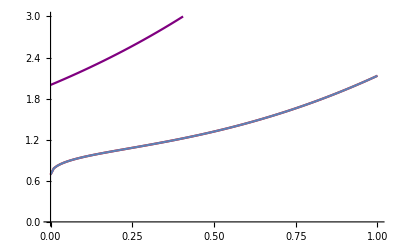

```mathematica
Show[ListLinePlot[dataquad,PlotStyle->Red,PlotRange->{{0,1},{0,3}}],ListLinePlot[Last@datasimple,PlotRange->{{0,1},{0,3}}],Plot[G[x],{x,0,1},PlotStyle->Purple,PlotRange->{{0,1},{0,3}}]]
```

```mathematica
(*eq={y[x]-λ∫_a^b k[x,s]*y[s]ⅆs==f[x]};
params = {a->0,b->1,k[x,s]->0.5(1-x *Cos[x *s]),f[x]->0.5(1+Sin[x])};
params1 = {a->0,b->1,k[x,s]->1,f[x]->0.5(1+Sin[x])};*)
```

```mathematica
(*eq=eq/.params;
DSolveValue[eq[[1]],y[x],x]*)
MaxNorm[data_,G_]:=Max[Table[Abs[G[data[[i,1]]]-data[[i,2]]],{i,1,Length@data}]];
```

```mathematica
errors2=Table[{i, MaxNorm[datasimple[[i]],G]},{i,1,Length@datasimple}];
```

```mathematica
logerrors=({#[[1]],Log[#[[2]]]})&/@errors2;
```

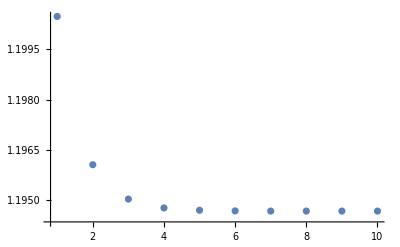

```mathematica
ListPlot[logerrors, PlotRange->Full]
```

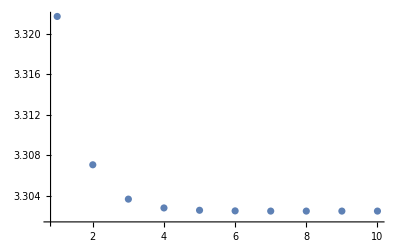

```mathematica
ListPlot[errors2, PlotRange->All]
```

```mathematica
Grid[{{"Iters","|err|"}}~Join~errors2, Frame->All, Spacings -> {1, 1}]
```

Iters | |err|
1 | 3.32172
2 | 3.30708
3 | 3.30369
4 | 3.30282
5 | 3.30259
6 | 3.30253
7 | 3.30251
8 | 3.30251
9 | 3.30251
10 | 3.30251

```mathematica
datah=Import["solution_h.dat"];
data2h=Import["solution_2h.dat"];
data4h=Import["solution_4h.dat"];
```

```mathematica
norms={{"h",MaxNorm[datah,G]},{"2h",MaxNorm[data2h,G]},{"4h",MaxNorm[data4h,G]}};
```

```mathematica
Grid[norms, Frame-> All, Spacings->{1, 1}]
```

h | 3.30252
2h | 3.30252
4h | 3.30251

#### Вырожденное ядро

```mathematica
datadegenerate =Flatten@ Import["solution_degenerate.dat"];
λ=1;
f [x_]:= √x+x^2;
```

```mathematica
Series[1-x*Cos[x*s],{x,0,20}]
```

1-x+(s^2 x^3)/2-(s^4 x^5)/24+(s^6 x^7)/720-(s^8 x^9)/40320+(s^10 x^11)/3628800-(s^12 x^13)/479001600+(s^14 x^15)/87178291200-(s^16 x^17)/20922789888000+(s^18 x^19)/6402373705728000+O[x]^21

```mathematica
Plot3D[{1-x,1-x+(s^2 x^3)/2,1-x+(s^2 x^3)/2-(s^4 x^5)/24,1-x+(s^2 x^3)/2-(s^4 x^5)/24+(s^6 x^7)/720-(s^8 x^9)/40320+(s^10 x^11)/3628800-(s^12 x^13)/479001600+(s^14 x^15)/87178291200-(s^16 x^17)/20922789888000+(s^18 x^19)/6402373705728000,1-x*Cos[x*s]},{x,0,1},{s,0,1}]
```

-Graphics3D-

```mathematica
u[x_]:=f[x]+(1-x)*λ*datadegenerate[[1]]+λ*Sum[datadegenerate[[i]]*(-1)^i x^(2i-1),{i,2,Length@datadegenerate}];
```

```mathematica
u[x]
```

0.77908 (1-x)+√x+x^2+0.217907 x^3-0.0124423 x^5+0.000315291 x^7-4.54076×10^-6 x^9+4.22691×10^-8 x^11-2.75497×10^-10 x^13+1.32806×10^-12 x^15-4.9284×10^-15 x^17+1.45162×10^-17 x^19

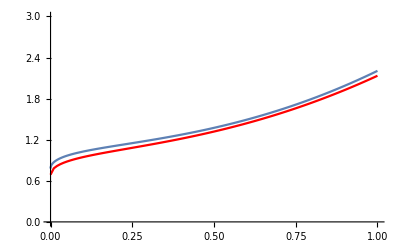

```mathematica
Show[Plot[u[x],{x,0,1},PlotRange->{{0,1},{0,3}}],ListLinePlot[dataquad,PlotStyle->Red,PlotRange->{{0,1},{0,3}}]]
```

#### Сингулярное ядро

```mathematica
datasingular = Import["solution_singular.dat"];
```

```mathematica
ListPointPlot3D[datasingular, AxesLabel->{"x", "y", "Res"},AxesOrigin->{0,0,0}]
```

-Graphics3D-